```mathematica
(*Integral for Furier*)
Integral = Integrate[x(λ*Cos[λ*x]- h*Sin[λ * x]), {x, 0, l}]
```

(-λ+(1+h l) λ Cos[l λ]+(-h+l λ^2) Sin[l λ])/λ^2

```mathematica
An = 2 / (l * λ^2 + h^2 * l - 2*h) * Integral
Bn = -2 / ((l * λ^2 + h^2 * l - 2*h)*a*λ) * Integral
```

(2 (-λ+(1+h l) λ Cos[l λ]+(-h+l λ^2) Sin[l λ]))/(λ^2 (-2 h+h^2 l+l λ^2))

-(2 (-λ+(1+h l) λ Cos[l λ]+(-h+l λ^2) Sin[l λ]))/(a λ^3 (-2 h+h^2 l+l λ^2))

```mathematica
FullSimplify[An]
FullSimplify[Bn]
```

(-2 λ+2 (1+h l) λ Cos[l λ]-2 (h-l λ^2) Sin[l λ])/(h (-2+h l) λ^2+l λ^4)

(2 (λ-(1+h l) λ Cos[l λ]+(h-l λ^2) Sin[l λ]))/(a h (-2+h l) λ^3+a l λ^5)

```mathematica
a =1;
h = 10;
l = 2;
```

```mathematica
root[n_]:= NSolve[Cot[2*x]==(x^2 - h^2)/(2*x*h) && 100*n<x≤100*(n+1),Reals];
list = {};

list = Join[list, Values[root[1]]]
len = list//Length
list[[1]]
```

{{100.63},{102.199},{103.769},{105.338},{106.907},{108.477},{110.046},{111.616},{113.185},{114.755},{116.325},{117.894},{119.464},{121.034},{122.603},{124.173},{125.743},{127.313},{128.883},{130.453},{132.022},{133.592},{135.162},{136.732},{138.302},{139.872},{141.442},{143.012},{144.582},{146.152},{147.722},{149.293},{150.863},{152.433},{154.003},{155.573},{157.143},{158.713},{160.284},{161.854},{163.424},{164.994},{166.564},{168.135},{169.705},{171.275},{172.845},{174.416},{175.986},{177.556},{179.127},{180.697},{182.267},{183.838},{185.408},{186.978},{188.549},{190.119},{191.689},{193.26},{194.83},{196.4},{197.971},{199.541}}

64

{100.63}

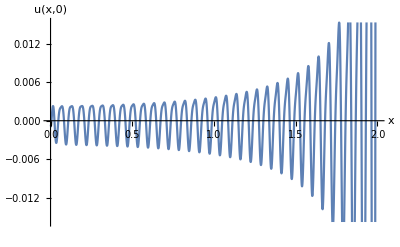

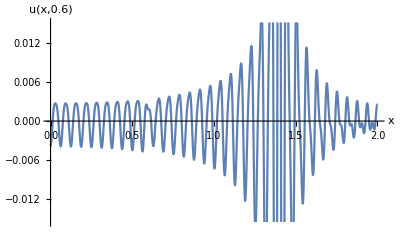

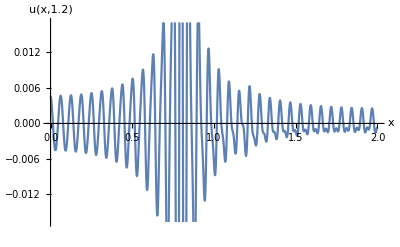

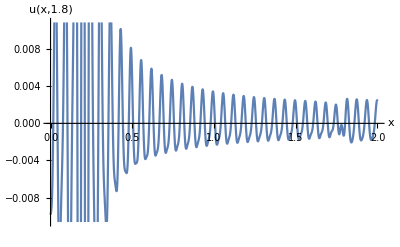

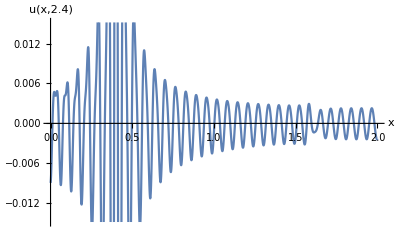

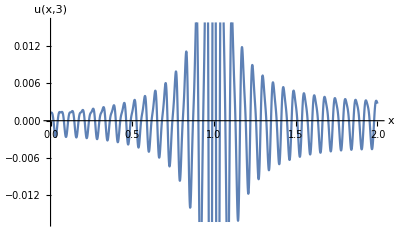

```mathematica
u[x_, t_] := Sum[((-2 * list[[k]] + 2(1 + h*l) * list[[k]]*Cos[list[[k]] * l] - 2 * (h - l * list[[k]]^2) * Sin[list[[k]] * l])/ (h * (h * l - 2)*list[[k]]^2 + l * list[[k]]^4) * Cos[a * list[[k]] * t] - (-2 * list[[k]] + 2(1 + h*l) * list[[k]]*Cos[list[[k]] * l] - 2 * (h - l * list[[k]]^2) * Sin[list[[k]] * l])/ (h * (h * l - 2)*list[[k]]^2 + l * list[[k]]^4 * a * list[[k]]) * Sin[a * list[[k]] * t])*(list[[k]] * Cos[list[[k]] * x] - h * Sin[list[[k]] * x]), {k, 1, len}]
Plot[Evaluate[u[x, 0 ]], {x, 0, l},  AxesLabel->{x, "u(x,0)" }]
Plot[Evaluate[u[x, 0.6 ]], {x, 0, l},  AxesLabel->{x, "u(x,0.6)" }]
Plot[Evaluate[u[x, 1.2]], {x, 0, l},  AxesLabel->{x, "u(x,1.2)" }]
Plot[Evaluate[u[x,  1.8]], {x, 0, l},  AxesLabel->{x, "u(x,1.8)" }]
Plot[Evaluate[u[x, 2.4 ]], {x, 0, l},  AxesLabel->{x, "u(x,2.4)" }]
Plot[Evaluate[u[x, 3 ]], {x, 0, l},  AxesLabel->{x, "u(x,3)" }]
```